## QCD Parameters

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

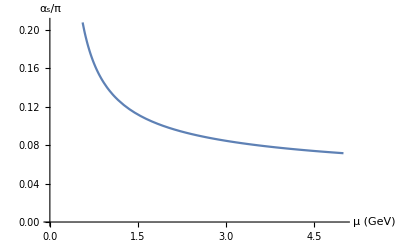

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

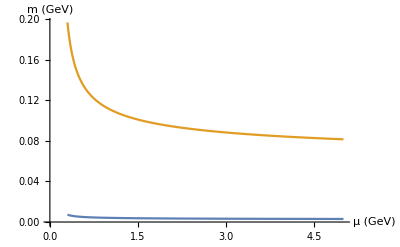

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (Central Values)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="central";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];
s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$6931626,r$6931626,y$6931626} and {z$6931626,r$6931626,y$6931626}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$6931626,r1$6931626,m2$6931626,r2$6931626} and {m1$6931626,r1$6931626,m2$6931626,r2$6931626}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$6931658,r$6931658,y$6931658} and {z$6931658,r$6931658,y$6931658}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$6958570,r$6958570,y$6958570} and {z$6958570,r$6958570,y$6958570}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$6958570,r1$6958570,m2$6958570,r2$6958570} and {m1$6958570,r1$6958570,m2$6958570,r2$6958570}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$6958602,r$6958602,y$6958602} and {z$6958602,r$6958602,y$6958602}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$6985514,r$6985514,y$6985514} and {z$6985514,r$6985514,y$6985514}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$6985514,r1$6985514,m2$6985514,r2$6985514} and {m1$6985514,r1$6985514,m2$6985514,r2$6985514}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$6985546,r$6985546,y$6985546} and {z$6985546,r$6985546,y$6985546}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7012458,r$7012458,y$7012458} and {z$7012458,r$7012458,y$7012458}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7012458,r1$7012458,m2$7012458,r2$7012458} and {m1$7012458,r1$7012458,m2$7012458,r2$7012458}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7012490,r$7012490,y$7012490} and {z$7012490,r$7012490,y$7012490}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7056033,r$7056033,y$7056033} and {z$7056033,r$7056033,y$7056033}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7056033,r1$7056033,m2$7056033,r2$7056033} and {m1$7056033,r1$7056033,m2$7056033,r2$7056033}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7056065,r$7056065,y$7056065} and {z$7056065,r$7056065,y$7056065}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7087177,r$7087177,y$7087177} and {z$7087177,r$7087177,y$7087177}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7087177,r1$7087177,m2$7087177,r2$7087177} and {m1$7087177,r1$7087177,m2$7087177,r2$7087177}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7087209,r$7087209,y$7087209} and {z$7087209,r$7087209,y$7087209}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7118321,r$7118321,y$7118321} and {z$7118321,r$7118321,y$7118321}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7118321,r1$7118321,m2$7118321,r2$7118321} and {m1$7118321,r1$7118321,m2$7118321,r2$7118321}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7118353,r$7118353,y$7118353} and {z$7118353,r$7118353,y$7118353}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7149465,r$7149465,y$7149465} and {z$7149465,r$7149465,y$7149465}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7149465,r1$7149465,m2$7149465,r2$7149465} and {m1$7149465,r1$7149465,m2$7149465,r2$7149465}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7149497,r$7149497,y$7149497} and {z$7149497,r$7149497,y$7149497}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters + 4D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075+0.02;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.779

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (+4D Gluon)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="upper4D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];
s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7200997,r$7200997,y$7200997} and {z$7200997,r$7200997,y$7200997}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7200997,r1$7200997,m2$7200997,r2$7200997} and {m1$7200997,r1$7200997,m2$7200997,r2$7200997}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7201029,r$7201029,y$7201029} and {z$7201029,r$7201029,y$7201029}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7227941,r$7227941,y$7227941} and {z$7227941,r$7227941,y$7227941}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7227941,r1$7227941,m2$7227941,r2$7227941} and {m1$7227941,r1$7227941,m2$7227941,r2$7227941}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7227973,r$7227973,y$7227973} and {z$7227973,r$7227973,y$7227973}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7254885,r$7254885,y$7254885} and {z$7254885,r$7254885,y$7254885}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7254885,r1$7254885,m2$7254885,r2$7254885} and {m1$7254885,r1$7254885,m2$7254885,r2$7254885}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7254917,r$7254917,y$7254917} and {z$7254917,r$7254917,y$7254917}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7281829,r$7281829,y$7281829} and {z$7281829,r$7281829,y$7281829}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7281829,r1$7281829,m2$7281829,r2$7281829} and {m1$7281829,r1$7281829,m2$7281829,r2$7281829}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7281861,r$7281861,y$7281861} and {z$7281861,r$7281861,y$7281861}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7324724,r$7324724,y$7324724} and {z$7324724,r$7324724,y$7324724}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7324724,r1$7324724,m2$7324724,r2$7324724} and {m1$7324724,r1$7324724,m2$7324724,r2$7324724}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7324756,r$7324756,y$7324756} and {z$7324756,r$7324756,y$7324756}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7355868,r$7355868,y$7355868} and {z$7355868,r$7355868,y$7355868}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7355868,r1$7355868,m2$7355868,r2$7355868} and {m1$7355868,r1$7355868,m2$7355868,r2$7355868}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7355900,r$7355900,y$7355900} and {z$7355900,r$7355900,y$7355900}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7387012,r$7387012,y$7387012} and {z$7387012,r$7387012,y$7387012}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7387012,r1$7387012,m2$7387012,r2$7387012} and {m1$7387012,r1$7387012,m2$7387012,r2$7387012}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7387044,r$7387044,y$7387044} and {z$7387044,r$7387044,y$7387044}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7418156,r$7418156,y$7418156} and {z$7418156,r$7418156,y$7418156}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7418156,r1$7418156,m2$7418156,r2$7418156} and {m1$7418156,r1$7418156,m2$7418156,r2$7418156}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7418188,r$7418188,y$7418188} and {z$7418188,r$7418188,y$7418188}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters - 4D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075-0.02;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.451

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (-4D Gluon)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="lower4D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7468886,r$7468886,y$7468886} and {z$7468886,r$7468886,y$7468886}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7468886,r1$7468886,m2$7468886,r2$7468886} and {m1$7468886,r1$7468886,m2$7468886,r2$7468886}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7468918,r$7468918,y$7468918} and {z$7468918,r$7468918,y$7468918}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7495830,r$7495830,y$7495830} and {z$7495830,r$7495830,y$7495830}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7495830,r1$7495830,m2$7495830,r2$7495830} and {m1$7495830,r1$7495830,m2$7495830,r2$7495830}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7495862,r$7495862,y$7495862} and {z$7495862,r$7495862,y$7495862}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7522774,r$7522774,y$7522774} and {z$7522774,r$7522774,y$7522774}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7522774,r1$7522774,m2$7522774,r2$7522774} and {m1$7522774,r1$7522774,m2$7522774,r2$7522774}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7522806,r$7522806,y$7522806} and {z$7522806,r$7522806,y$7522806}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7549718,r$7549718,y$7549718} and {z$7549718,r$7549718,y$7549718}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7549718,r1$7549718,m2$7549718,r2$7549718} and {m1$7549718,r1$7549718,m2$7549718,r2$7549718}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7549750,r$7549750,y$7549750} and {z$7549750,r$7549750,y$7549750}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7592566,r$7592566,y$7592566} and {z$7592566,r$7592566,y$7592566}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7592566,r1$7592566,m2$7592566,r2$7592566} and {m1$7592566,r1$7592566,m2$7592566,r2$7592566}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7592598,r$7592598,y$7592598} and {z$7592598,r$7592598,y$7592598}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7623710,r$7623710,y$7623710} and {z$7623710,r$7623710,y$7623710}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7623710,r1$7623710,m2$7623710,r2$7623710} and {m1$7623710,r1$7623710,m2$7623710,r2$7623710}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7623742,r$7623742,y$7623742} and {z$7623742,r$7623742,y$7623742}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7654854,r$7654854,y$7654854} and {z$7654854,r$7654854,y$7654854}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7654854,r1$7654854,m2$7654854,r2$7654854} and {m1$7654854,r1$7654854,m2$7654854,r2$7654854}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7654886,r$7654886,y$7654886} and {z$7654886,r$7654886,y$7654886}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7685998,r$7685998,y$7685998} and {z$7685998,r$7685998,y$7685998}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7685998,r1$7685998,m2$7685998,r2$7685998} and {m1$7685998,r1$7685998,m2$7685998,r2$7685998}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7686030,r$7686030,y$7686030} and {z$7686030,r$7686030,y$7686030}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters + 6D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2+1) αGG
```

0.69

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (+6D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="upper6D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7737522,r$7737522,y$7737522} and {z$7737522,r$7737522,y$7737522}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7737522,r1$7737522,m2$7737522,r2$7737522} and {m1$7737522,r1$7737522,m2$7737522,r2$7737522}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7737554,r$7737554,y$7737554} and {z$7737554,r$7737554,y$7737554}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7764466,r$7764466,y$7764466} and {z$7764466,r$7764466,y$7764466}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7764466,r1$7764466,m2$7764466,r2$7764466} and {m1$7764466,r1$7764466,m2$7764466,r2$7764466}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7764498,r$7764498,y$7764498} and {z$7764498,r$7764498,y$7764498}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7791410,r$7791410,y$7791410} and {z$7791410,r$7791410,y$7791410}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7791410,r1$7791410,m2$7791410,r2$7791410} and {m1$7791410,r1$7791410,m2$7791410,r2$7791410}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7791442,r$7791442,y$7791442} and {z$7791442,r$7791442,y$7791442}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7818354,r$7818354,y$7818354} and {z$7818354,r$7818354,y$7818354}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7818354,r1$7818354,m2$7818354,r2$7818354} and {m1$7818354,r1$7818354,m2$7818354,r2$7818354}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7818386,r$7818386,y$7818386} and {z$7818386,r$7818386,y$7818386}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7861257,r$7861257,y$7861257} and {z$7861257,r$7861257,y$7861257}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7861257,r1$7861257,m2$7861257,r2$7861257} and {m1$7861257,r1$7861257,m2$7861257,r2$7861257}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7861289,r$7861289,y$7861289} and {z$7861289,r$7861289,y$7861289}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7892401,r$7892401,y$7892401} and {z$7892401,r$7892401,y$7892401}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7892401,r1$7892401,m2$7892401,r2$7892401} and {m1$7892401,r1$7892401,m2$7892401,r2$7892401}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7892433,r$7892433,y$7892433} and {z$7892433,r$7892433,y$7892433}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7923545,r$7923545,y$7923545} and {z$7923545,r$7923545,y$7923545}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7923545,r1$7923545,m2$7923545,r2$7923545} and {m1$7923545,r1$7923545,m2$7923545,r2$7923545}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7923577,r$7923577,y$7923577} and {z$7923577,r$7923577,y$7923577}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$7954689,r$7954689,y$7954689} and {z$7954689,r$7954689,y$7954689}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$7954689,r1$7954689,m2$7954689,r2$7954689} and {m1$7954689,r1$7954689,m2$7954689,r2$7954689}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$7954721,r$7954721,y$7954721} and {z$7954721,r$7954721,y$7954721}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters - 6D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (-6D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="lower6D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8006227,r$8006227,y$8006227} and {z$8006227,r$8006227,y$8006227}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8006227,r1$8006227,m2$8006227,r2$8006227} and {m1$8006227,r1$8006227,m2$8006227,r2$8006227}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8006259,r$8006259,y$8006259} and {z$8006259,r$8006259,y$8006259}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8033171,r$8033171,y$8033171} and {z$8033171,r$8033171,y$8033171}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8033171,r1$8033171,m2$8033171,r2$8033171} and {m1$8033171,r1$8033171,m2$8033171,r2$8033171}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8033203,r$8033203,y$8033203} and {z$8033203,r$8033203,y$8033203}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8060115,r$8060115,y$8060115} and {z$8060115,r$8060115,y$8060115}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8060115,r1$8060115,m2$8060115,r2$8060115} and {m1$8060115,r1$8060115,m2$8060115,r2$8060115}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8060147,r$8060147,y$8060147} and {z$8060147,r$8060147,y$8060147}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8087059,r$8087059,y$8087059} and {z$8087059,r$8087059,y$8087059}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8087059,r1$8087059,m2$8087059,r2$8087059} and {m1$8087059,r1$8087059,m2$8087059,r2$8087059}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8087091,r$8087091,y$8087091} and {z$8087091,r$8087091,y$8087091}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8130646,r$8130646,y$8130646} and {z$8130646,r$8130646,y$8130646}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8130646,r1$8130646,m2$8130646,r2$8130646} and {m1$8130646,r1$8130646,m2$8130646,r2$8130646}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8130678,r$8130678,y$8130678} and {z$8130678,r$8130678,y$8130678}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8161790,r$8161790,y$8161790} and {z$8161790,r$8161790,y$8161790}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8161790,r1$8161790,m2$8161790,r2$8161790} and {m1$8161790,r1$8161790,m2$8161790,r2$8161790}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8161822,r$8161822,y$8161822} and {z$8161822,r$8161822,y$8161822}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8192934,r$8192934,y$8192934} and {z$8192934,r$8192934,y$8192934}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8192934,r1$8192934,m2$8192934,r2$8192934} and {m1$8192934,r1$8192934,m2$8192934,r2$8192934}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8192966,r$8192966,y$8192966} and {z$8192966,r$8192966,y$8192966}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8224078,r$8224078,y$8224078} and {z$8224078,r$8224078,y$8224078}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8224078,r1$8224078,m2$8224078,r2$8224078} and {m1$8224078,r1$8224078,m2$8224078,r2$8224078}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8224110,r$8224110,y$8224110} and {z$8224110,r$8224110,y$8224110}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters + 3D Quark Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)+0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)+0.0042}
```

-0.0000892155

-0.00160179

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2) αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (+3D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="upper3D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8274684,r$8274684,y$8274684} and {z$8274684,r$8274684,y$8274684}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8274684,r1$8274684,m2$8274684,r2$8274684} and {m1$8274684,r1$8274684,m2$8274684,r2$8274684}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8274716,r$8274716,y$8274716} and {z$8274716,r$8274716,y$8274716}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8301712,r$8301712,y$8301712} and {z$8301712,r$8301712,y$8301712}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8301712,r1$8301712,m2$8301712,r2$8301712} and {m1$8301712,r1$8301712,m2$8301712,r2$8301712}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8301744,r$8301744,y$8301744} and {z$8301744,r$8301744,y$8301744}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8328719,r$8328719,y$8328719} and {z$8328719,r$8328719,y$8328719}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8328719,r1$8328719,m2$8328719,r2$8328719} and {m1$8328719,r1$8328719,m2$8328719,r2$8328719}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8328751,r$8328751,y$8328751} and {z$8328751,r$8328751,y$8328751}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8355726,r$8355726,y$8355726} and {z$8355726,r$8355726,y$8355726}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8355726,r1$8355726,m2$8355726,r2$8355726} and {m1$8355726,r1$8355726,m2$8355726,r2$8355726}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8355758,r$8355758,y$8355758} and {z$8355758,r$8355758,y$8355758}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8399532,r$8399532,y$8399532} and {z$8399532,r$8399532,y$8399532}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8399532,r1$8399532,m2$8399532,r2$8399532} and {m1$8399532,r1$8399532,m2$8399532,r2$8399532}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8399564,r$8399564,y$8399564} and {z$8399564,r$8399564,y$8399564}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8431964,r$8431964,y$8431964} and {z$8431964,r$8431964,y$8431964}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8431964,r1$8431964,m2$8431964,r2$8431964} and {m1$8431964,r1$8431964,m2$8431964,r2$8431964}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8431996,r$8431996,y$8431996} and {z$8431996,r$8431996,y$8431996}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8464410,r$8464410,y$8464410} and {z$8464410,r$8464410,y$8464410}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8464410,r1$8464410,m2$8464410,r2$8464410} and {m1$8464410,r1$8464410,m2$8464410,r2$8464410}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8464442,r$8464442,y$8464442} and {z$8464442,r$8464442,y$8464442}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8496863,r$8496863,y$8496863} and {z$8496863,r$8496863,y$8496863}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8496863,r1$8496863,m2$8496863,r2$8496863} and {m1$8496863,r1$8496863,m2$8496863,r2$8496863}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8496895,r$8496895,y$8496895} and {z$8496895,r$8496895,y$8496895}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters - 3D Quark Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)-0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)-0.0042}
```

-0.0000766423

-0.00137567

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (-3D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="lower3D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8550011,r$8550011,y$8550011} and {z$8550011,r$8550011,y$8550011}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8550011,r1$8550011,m2$8550011,r2$8550011} and {m1$8550011,r1$8550011,m2$8550011,r2$8550011}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8550043,r$8550043,y$8550043} and {z$8550043,r$8550043,y$8550043}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8577074,r$8577074,y$8577074} and {z$8577074,r$8577074,y$8577074}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8577074,r1$8577074,m2$8577074,r2$8577074} and {m1$8577074,r1$8577074,m2$8577074,r2$8577074}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8577106,r$8577106,y$8577106} and {z$8577106,r$8577106,y$8577106}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8604109,r$8604109,y$8604109} and {z$8604109,r$8604109,y$8604109}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8604109,r1$8604109,m2$8604109,r2$8604109} and {m1$8604109,r1$8604109,m2$8604109,r2$8604109}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8604141,r$8604141,y$8604141} and {z$8604141,r$8604141,y$8604141}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8631130,r$8631130,y$8631130} and {z$8631130,r$8631130,y$8631130}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8631130,r1$8631130,m2$8631130,r2$8631130} and {m1$8631130,r1$8631130,m2$8631130,r2$8631130}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8631162,r$8631162,y$8631162} and {z$8631162,r$8631162,y$8631162}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8674983,r$8674983,y$8674983} and {z$8674983,r$8674983,y$8674983}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8674983,r1$8674983,m2$8674983,r2$8674983} and {m1$8674983,r1$8674983,m2$8674983,r2$8674983}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8675015,r$8675015,y$8675015} and {z$8675015,r$8675015,y$8675015}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8706386,r$8706386,y$8706386} and {z$8706386,r$8706386,y$8706386}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8706386,r1$8706386,m2$8706386,r2$8706386} and {m1$8706386,r1$8706386,m2$8706386,r2$8706386}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8706418,r$8706418,y$8706418} and {z$8706418,r$8706418,y$8706418}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8737684,r$8737684,y$8737684} and {z$8737684,r$8737684,y$8737684}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8737684,r1$8737684,m2$8737684,r2$8737684} and {m1$8737684,r1$8737684,m2$8737684,r2$8737684}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8737716,r$8737716,y$8737716} and {z$8737716,r$8737716,y$8737716}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8769003,r$8769003,y$8769003} and {z$8769003,r$8769003,y$8769003}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8769003,r1$8769003,m2$8769003,r2$8769003} and {m1$8769003,r1$8769003,m2$8769003,r2$8769003}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8769035,r$8769035,y$8769035} and {z$8769035,r$8769035,y$8769035}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters + 5D Mixed Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√(0.8+0.1)
```

0.948683

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.8 qq

1.8 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2) αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (+5D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="upper5D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8820036,r$8820036,y$8820036} and {z$8820036,r$8820036,y$8820036}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8820036,r1$8820036,m2$8820036,r2$8820036} and {m1$8820036,r1$8820036,m2$8820036,r2$8820036}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8820068,r$8820068,y$8820068} and {z$8820068,r$8820068,y$8820068}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8847155,r$8847155,y$8847155} and {z$8847155,r$8847155,y$8847155}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8847155,r1$8847155,m2$8847155,r2$8847155} and {m1$8847155,r1$8847155,m2$8847155,r2$8847155}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8847187,r$8847187,y$8847187} and {z$8847187,r$8847187,y$8847187}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8874246,r$8874246,y$8874246} and {z$8874246,r$8874246,y$8874246}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8874246,r1$8874246,m2$8874246,r2$8874246} and {m1$8874246,r1$8874246,m2$8874246,r2$8874246}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8874278,r$8874278,y$8874278} and {z$8874278,r$8874278,y$8874278}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8901351,r$8901351,y$8901351} and {z$8901351,r$8901351,y$8901351}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8901351,r1$8901351,m2$8901351,r2$8901351} and {m1$8901351,r1$8901351,m2$8901351,r2$8901351}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8901383,r$8901383,y$8901383} and {z$8901383,r$8901383,y$8901383}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8944430,r$8944430,y$8944430} and {z$8944430,r$8944430,y$8944430}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8944430,r1$8944430,m2$8944430,r2$8944430} and {m1$8944430,r1$8944430,m2$8944430,r2$8944430}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8944462,r$8944462,y$8944462} and {z$8944462,r$8944462,y$8944462}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$8975686,r$8975686,y$8975686} and {z$8975686,r$8975686,y$8975686}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$8975686,r1$8975686,m2$8975686,r2$8975686} and {m1$8975686,r1$8975686,m2$8975686,r2$8975686}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$8975718,r$8975718,y$8975718} and {z$8975718,r$8975718,y$8975718}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9006928,r$9006928,y$9006928} and {z$9006928,r$9006928,y$9006928}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9006928,r1$9006928,m2$9006928,r2$9006928} and {m1$9006928,r1$9006928,m2$9006928,r2$9006928}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9006960,r$9006960,y$9006960} and {z$9006960,r$9006960,y$9006960}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9038170,r$9038170,y$9038170} and {z$9038170,r$9038170,y$9038170}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9038170,r1$9038170,m2$9038170,r2$9038170} and {m1$9038170,r1$9038170,m2$9038170,r2$9038170}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9038202,r$9038202,y$9038202} and {z$9038202,r$9038202,y$9038202}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

## QCD Parameters - 5D Mixed Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√(0.8-0.1)
```

0.83666

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.4 qq

1.4 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02) - no 6D Gluon Condensate

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
(*e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];*)f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_,s0_,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_,s0_,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (-5D)

```mathematica
(*BEGIN PARAMETERS*)
errChannel="lower5D";
jpcTable={"0+-"};
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
flavorTable={"light","strange"};
tauList=Table[τ,{τ,15,20,Abs[15-20]/10}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{23.897000000000002, 13.789, 23.975, 13.801},flavor=="light"},{{23.025000000000002, 13.116, 24.819, 13.393},flavor=="strange"}}]
(*END PARAMETERS*)
```

```mathematica
(*BEGIN FUNCTION DEFINITIONS*)
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{gaussian[0,s,τ,s0,jpc,flavor],s>0},s,MaxIterations->175]
A[k_,τ_,s0_,jpc_,flavor_]:=momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor]-3(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+2(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^3
S[k_,τ_,s0_,jpc_,flavor_]:=(momentN[4,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])-4(momentN[3,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])+6(momentN[2,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^2-3(momentN[1,k,τ,s0,jpc,flavor]/moment0[k,τ,s0,jpc,flavor])^4
DNRParameterSolve[τ_,s0_?NumericQ,jpc_,flavor_]:=Quiet[Module[{z,r,y,m1,r1,m2,r2},{z,r,y}={z,r,y}/.Solve[{momentN[1,0,τ,s0,jpc,flavor]/moment0[0,τ,s0,jpc,flavor]==1/2(z+r y),σSqrd[τ,s0,jpc,flavor]-2τ == 1/4 y^2(1-r^2),A[0,τ,s0,jpc,flavor]==-1/4 y^3 r(1-r^2)},{z,r,y}][[2]];
{m1,r1,m2,r2}={m1,r1,m2,r2}/.Solve[{z==m1^2+m2^2,y==m1^2-m2^2,r==r1-r2,r1+r2==1,m1>0,m2>0,r1>0,r2>0},{m1,r1,m2,r2}][[1]];
{m1,r1,m2,r2}],Solve::ratnz]
(* Using k = 0 *)
model[s_,τ_,m1_,r1_,m2_,r2_]:=(1/Sqrt[4τ π ])(r1 Exp[(-(s-(m1)^2)^2)/(4τ)]+r2 Exp[(-(s-(m2)^2)^2)/(4τ)])

adherancePlot[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{τ,S[0,τ,s0optimized,jpc,flavor],12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2),S[0,τ,s0optimized,jpc,flavor]-(12 τ^2+12τ(σSqrd[τ,s0optimized,jpc,flavor]-2τ)+1/16(m1^2-m2^2)^4(1-(r1-r2)^2)(1+3(r1-r2)^2))},{τ,1,26}]
]

modelCompare[tau_,s0optimized_,jpc_,flavor_]:=Module[{m1,m2,r1,r2},
{m1,r1,m2,r2}=DNRParameterSolve[tau,s0optimized,jpc,flavor];
Parallelize@Table[{s,Evaluate@normGaussian[s,tau,s0optimized,jpc,flavor],model[s,tau,m1,r1,m2,r2]},{s,-5,30}]
]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
(*BEGIN LOOP*)
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=Parallelize[First[SortBy[Table[{s0,DNRParameterSolve[15,s0,jpc,flavor][[2]]},{s0,5,35,0.01}],Last]
][[1]]
];

s0optimizedList[flavor]=Append[s0optimizedList[flavor],s0optimized];

mass1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[1]],DNRParameterSolve[20,s0,jpc,flavor][[1]]},{s0,0,50}];
coupling1plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[2]],DNRParameterSolve[20,s0,jpc,flavor][[2]]},{s0,0,50}];
mass2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[3]],DNRParameterSolve[20,s0,jpc,flavor][[3]]},{s0,0,50}];
coupling2plots=Parallelize@Table[{s0,DNRParameterSolve[15,s0,jpc,flavorTable[[j]]][[4]],DNRParameterSolve[20,s0,jpc,flavor][[4]]},{s0,0,50}];
massSplit=Parallelize@Table[{τ,DNRParameterSolve[τ,s0optimized,jpc,flavor][[1]],DNRParameterSolve[τ,s0optimized,jpc,flavor][[3]]},{τ,15,20,Abs[15-20]/10}];
dnrAdherance=adherancePlot[15,s0optimized,jpc,flavor];
modelComparison=modelCompare[15,s0optimized,jpc,flavor];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r1Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling1plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-m2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=mass2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-r2Plots-",ToString[flavor],"_",
ToString[jpc],ToString[errChannel]];
input=coupling2plots;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-massSplit-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=massSplit;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-dnrAdherance-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=dnrAdherance;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-modelComparison-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=modelComparison;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];

Clear[filename,input];
filename=StringJoin[DateString["ISODate"],"-s0Value-",ToString[flavor],"_",ToString[jpc],ToString[errChannel]];
input=s0optimized;
Put[filename];
PutAppend[input,filename];
Clear[filename,input];
];
]
(*END LOOP*)
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9090109,r$9090109,y$9090109} and {z$9090109,r$9090109,y$9090109}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9090109,r1$9090109,m2$9090109,r2$9090109} and {m1$9090109,r1$9090109,m2$9090109,r2$9090109}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9090141,r$9090141,y$9090141} and {z$9090141,r$9090141,y$9090141}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9117179,r$9117179,y$9117179} and {z$9117179,r$9117179,y$9117179}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9117179,r1$9117179,m2$9117179,r2$9117179} and {m1$9117179,r1$9117179,m2$9117179,r2$9117179}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9117211,r$9117211,y$9117211} and {z$9117211,r$9117211,y$9117211}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9144207,r$9144207,y$9144207} and {z$9144207,r$9144207,y$9144207}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9144207,r1$9144207,m2$9144207,r2$9144207} and {m1$9144207,r1$9144207,m2$9144207,r2$9144207}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9144239,r$9144239,y$9144239} and {z$9144239,r$9144239,y$9144239}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9171256,r$9171256,y$9171256} and {z$9171256,r$9171256,y$9171256}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9171256,r1$9171256,m2$9171256,r2$9171256} and {m1$9171256,r1$9171256,m2$9171256,r2$9171256}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9171288,r$9171288,y$9171288} and {z$9171288,r$9171288,y$9171288}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9215048,r$9215048,y$9215048} and {z$9215048,r$9215048,y$9215048}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9215048,r1$9215048,m2$9215048,r2$9215048} and {m1$9215048,r1$9215048,m2$9215048,r2$9215048}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9215080,r$9215080,y$9215080} and {z$9215080,r$9215080,y$9215080}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9247508,r$9247508,y$9247508} and {z$9247508,r$9247508,y$9247508}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9247508,r1$9247508,m2$9247508,r2$9247508} and {m1$9247508,r1$9247508,m2$9247508,r2$9247508}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9247540,r$9247540,y$9247540} and {z$9247540,r$9247540,y$9247540}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9280003,r$9280003,y$9280003} and {z$9280003,r$9280003,y$9280003}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9280003,r1$9280003,m2$9280003,r2$9280003} and {m1$9280003,r1$9280003,m2$9280003,r2$9280003}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9280035,r$9280035,y$9280035} and {z$9280035,r$9280035,y$9280035}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 2 of {} does not exist.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {z$9312526,r$9312526,y$9312526} and {z$9312526,r$9312526,y$9312526}/.{}⟦2⟧ are not the same shape.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {m1$9312526,r1$9312526,m2$9312526,r2$9312526} and {m1$9312526,r1$9312526,m2$9312526,r2$9312526}/.{}⟦1⟧ are not the same shape.

Part::partw: Part 2 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {z$9312558,r$9312558,y$9312558} and {z$9312558,r$9312558,y$9312558}/.{}⟦2⟧ are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.